```mathematica
Needs["JLink`"];
AddToClassPath["/Users/Hunter/Development/Wolfram Mathematica/javaplex-4.3.4/dist/javaplex/library/javaplex.jar"];
Plex4=LoadJavaClass["edu.stanford.math.plex4.api.Plex4"];
(*PointCloudEx=LoadJavaClass["edu.stanford.math.plex4.examples.PointCloudExamples"];
BarCodeCollection=LoadJavaClass["edu.stanford.math.plex4.homology.barcodes.BarcodeCollection"];
JPSimplex=LoadJavaClass["edu.stanford.math.plex4.homology.chain_basis.Simplex"];
AbstractPersistenceAlgorithm=LoadJavaClass["edu.stanford.math.plex4.homology.interfaces.AbstractPersistenceAlgorithm"];
EuclideanMetricSpace=LoadJavaClass["edu.stanford.math.plex4.metric.impl.EuclideanMetricSpace"];
LandmarkSelector=LoadJavaClass["edu.stanford.math.plex4.metric.landmark.LandmarkSelector"];
MaxMinLandmarkSelector=LoadJavaClass["edu.stanford.math.plex4.metric.landmark.MaxMinLandmarkSelector"];
LazyWitnessStream=LoadJavaClass["edu.stanford.math.plex4.streams.impl.LazyWitnessStream"];
Plex4=LoadJavaClass["edu.stanford.math.plex4.api.Plex4"];*)
```

```mathematica
AddToClassPath["/Users/Hunter/Development/Wolfram Mathematica/"];
MathematicaHelper = LoadJavaClass["myhelpers.MathematicaHelper"];
```

```mathematica
stream = Plex4`createExplicitSimplexStream[]
```

«JavaObject[edu.stanford.math.plex4.streams.impl.ExplicitSimplexStream]»

```mathematica
stream@addVertex[0]
stream@addVertex[1]
stream@addVertex[2]
(*stream@addElement[(0,1)]
stream@addElement[(2,1)]
stream@addElement[(0,2)]*)
stream@addElement[{0,1}]
stream@addElement[{2,1}]
stream@addElement[{0,2}]
stream@addElement[{0,1,2}]

stream@finalizeStream[]
```

```mathematica
num_simplices = stream@getSize[]
```

7

```mathematica
num_simplices
```

```mathematica
persistence = Plex4`getModularSimplicialAlgorithm[3,2]
```

«JavaObject[edu.stanford.math.plex4.autogen.homology.IntAbsoluteHomology]»

```mathematica
intervals = persistence@computeIntervals[stream]
output = intervals@toString[]
```

«JavaObject[edu.stanford.math.plex4.homology.barcodes.BarcodeCollection]»

Dimension: 0
[0.0, infinity)

```mathematica
intervals = persistence@computeAnnotatedIntervals[stream]
output  = intervals@toString[]
```

«JavaObject[edu.stanford.math.plex4.homology.barcodes.AnnotatedBarcodeCollection]»

Dimension: 0
[0.0, infinity): [0]

```mathematica
"Dimension: 0\n[0.0, infinity): [0]\nDimension: 1\n[0.0, infinity): [1,2] + [0,2] + [0,1]\n\n"
```

Dimension: 0
[0.0, infinity): [0]
Dimension: 1
[0.0, infinity): [1,2] + [0,2] + [0,1]

```mathematica
dimension=9
stream=Plex4`createExplicitSimplexStream[]
stream@addElement[Table[i, {i,0,dimension +1}]]
```

9

«JavaObject[edu.stanford.math.plex4.streams.impl.ExplicitSimplexStream]»

```mathematica
stream@ensureAllFaces[]
stream@removeElementIfPresent[Table[i,{i,0,dimension+1}]]
stream@finalizeStream[]
```

True

```mathematica
num_sim  = stream@getSize[]
```

2046

```mathematica
persistence = Plex4`getModularSimplicialAlgorithm[dimension+1, 2]
```

«JavaObject[edu.stanford.math.plex4.autogen.homology.IntAbsoluteHomology]»

```mathematica
intervals = persistence@computeIntervals[stream]@toString[]
```

Dimension: 0
[0.0, infinity)
Dimension: 9
[0.0, infinity)

```mathematica
stream=Plex4`createExplicitSimplexStream[]
```

«JavaObject[edu.stanford.math.plex4.streams.impl.ExplicitSimplexStream]»

```mathematica
stream@addVertex[1,0]
stream@addVertex[2,0]
stream@addVertex[3,0]
stream@addVertex[4,0]
stream@addVertex[5,1]
stream@addElement[{1,2},0]
stream@addElement[{2,3},0]
stream@addElement[{3,4},0]
stream@addElement[{4,1},0]
stream@addElement[{3,5},2]
stream@addElement[{4,5},3]
stream@addElement[{3,4,5},7]
stream@finalizeStream[]
```

```mathematica
persistence = Plex4`getModularSimplicialAlgorithm[3,2]
intervals = persistence@computeAnnotatedIntervals[stream]@toString[]
```

«JavaObject[edu.stanford.math.plex4.autogen.homology.IntAbsoluteHomology]»

Dimension: 0
[1.0, 2.0): -[3] + [5]
[0.0, infinity): [1]
Dimension: 1
[3.0, 7.0): [4,5] + [3,4] + -[3,5]
[0.0, infinity): [1,4] + [2,3] + [1,2] + [3,4]

```mathematica
list={{-1,0},{1,0},{1,2},{-1,2},{0,3}};

javaArray=MakeJavaObject[list];
javaArray

m_space = Plex4`createEuclideanMetricSpace[list]
m_space@getPoint[0]@toString[]
```

«JavaObject[[[I]»

«JavaObject[edu.stanford.math.plex4.metric.impl.EuclideanMetricSpace]»

m_space[getPoint[0][toString[]]]

```mathematica
Grid[{{-1,0},{1,0},{1,2},{-1,2},{0,3}}]
```

-1 | 0
1 | 0
1 | 2
-1 | 2
0 | 3

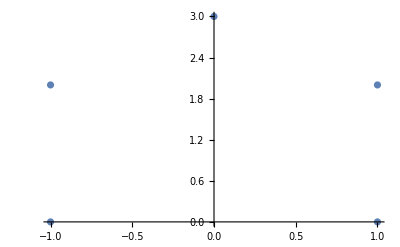

```mathematica
ListPlot[First[Grid[{{-1,0},{1,0},{1,2},{-1,2},{0,3}}]]]
```

```mathematica
sphere = PointCloudEx@getRandomTorusPoints[2000,1,2]
```

JavaClass[edu.stanford.math.plex4.examples.PointCloudExamples,<>][getRandomTorusPoints[2000,1,2][toString[]]]

```mathematica
distances={{0,2,Sqrt[8],2,Sqrt[10]},{2,0,2,Sqrt[8],Sqrt[10]},{Sqrt[8],2,0,2,Sqrt[2]},{2,Sqrt[8],2,0,Sqrt[2]},{Sqrt[10],Sqrt[10],Sqrt[2],Sqrt[2],0}}
```

{{0,2,2 √2,2,√10},{2,0,2,2 √2,√10},{2 √2,2,0,2,√2},{2,2 √2,2,0,√2},{√10,√10,√2,√2,0}}

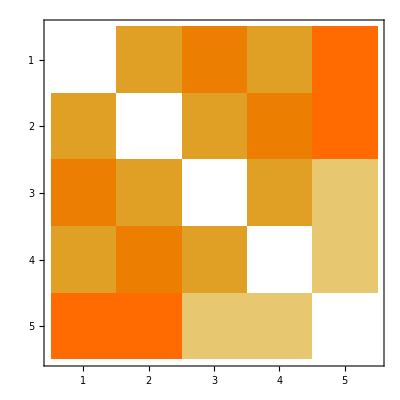

```mathematica
MatrixPlot[distances]
```

```mathematica
(*EuclideanMetricSpace=LoadJavaClass["edu.stanford.math.plex4.metric.impl.EuclideanMetricSpace"]*)
metric=LoadJavaClass["edu.stanford.math.plex4.metric.impl.ExplicitMetricSpace"]
```

JavaClass[edu.stanford.math.plex4.metric.impl.ExplicitMetricSpace,<>]